```mathematica
points=Import["~/Desktop/Bounce/points.csv"];
```

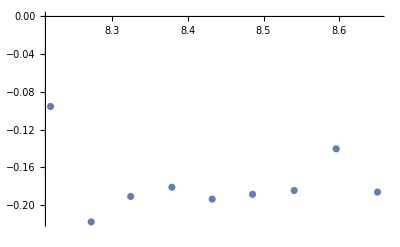

```mathematica
ts = points[[All,4]];
pts = points[[All,1;;3]];
vs = Differences[pts]/Differences[ts];
indicies =Position[Differences[Sign[Differences[pts[[All,3]]]]],_?(#>0&)]//Flatten;
runs=Table[pts[[indicies[[i-1]]+2;;indicies[[i]]-1]],{i,2,Length[indicies]}];
truns=Table[ts[[indicies[[i-1]]+2;;indicies[[i]]-1]],{i,2,Length[indicies]}];
runs =runs[[12;;,All,All]];
truns=truns[[12;;,All]];
txRuns = Table[Transpose[{truns[[i]],runs[[i,All,1]]}],{i,1,Length[runs]}];
tyRuns = Table[Transpose[{truns[[i]],runs[[i,All,1]]}],{i,1,Length[runs]}];
tzRuns = Table[Transpose[{truns[[i]],runs[[i,All,1]]}],{i,1,Length[runs]}];
ListPlot[txRuns[[7]]]
```